```mathematica
(* Global Reqresentation Space (GRS) ; 
   θY A q Subscript[y, 0] d Bo lgc ;              1  2 3 4  5  6  7; *)
```

```mathematica
zero[q_?NumberQ,y0_?NumberQ,Lnum_?NumberQ]:=Block[
{sol,s,y,a,x,θ},
sol=NDSolve[
{y'[s]==Sin[θ[s]],
x'[s]==Cos[θ[s]],
a'[s]==(-2*y[s])*Cos[θ[s]],
θ'[s]==q-y[s]*Bonum,

a[0]==0,
x[0]== 0,
θ[0]== 0,
y[0]==y0},

{y[s],a[s],θ[s],x[s]},{s,0,Lnum}
];

(*conditions de bords*)
{y[s],a[s]-Anum,x[s] - dnum}/.sol[[1]]/.s->Lnum
]
```

```mathematica
Anum=3.141592653589793;
dnum= Sqrt[1.004^2 - (1.74/2.)^2];
Bonum=0.5;
Lnum=2.72397295504927;
grsdepart={0.1,Anum,0.15521795561616364,-2.162609719677938,dnum,Bonum,Lnum};
listeGRS2Dpinning={grsdepart};
LastptFind=listeGRS2Dpinning[[-1]];
qapprox=LastptFind[[3]];
y0approx=LastptFind[[4]];
erreur=Total[Abs[zero[qapprox,y0approx,Lnum]]];
Print["Err: ",erreur];
```

Err: 1.23439×10^-7

```mathematica
fr=FindRoot[zero[q,y0,L],{q,qapprox},{y0,y0approx},{L,Lnum},
MaxIterations->30,
Jacobian->"FiniteDifference",
Method->{"Newton", "UpdateJacobian"->1}];
erreur=Total[Abs[zero[q/.fr,y0/.fr,L/.fr]]];
Print["Err2: ",erreur];
AppendTo[listeGRS2Dpinning,{0.1,Anum,q,y0,dnum,Bonum,L}/.fr]
```

Err2: 2.09411×10^-14

{{0.1,3.14159,0.155218,-2.16261,0.501115,0.5,2.72397},{0.1,3.14159,0.155218,-2.16261,0.501115,0.5,2.72397}}

```mathematica
(* Global Reqresentation Sqace (GRS) ; 
   θY A q Subscript[y, 0] d lgc ;              1  2 3 4  5  6  ; *)
```

```mathematica
imax=10;
Boinit=Bonum;
Bofin= 0.7;
Do[
Bonum=Boinit+(Bofin-Boinit)*i/imax;
fr=FindRoot[zero[q,y0,L],{q,qapprox},{y0,y0approx},{L,Lnum},
MaxIterations->30,
Jacobian->"FiniteDifference",
Method->{"Newton", "UpdateJacobian"->1}];
erreur=Total[Abs[zero[q/.fr,y0/.fr,L/.fr]]];
Print["Err2: ",erreur];
AppendTo[listeGRS2Dpinning,{0.1,Anum,q,y0,dnum,Bonum,L}/.fr]
,


{i,1,imax}]
```

```mathematica
listeGRS2Dpinning
```

Verifier le forme

```mathematica
(* Global Reqresentation Space (GRS) ; 
   θY A q Subscript[y, 0] d Bo lgc ;              1  2 3 4  5  6  7; *)
listplot={0.1,3.141592653589793,-0.26808573589218243,-2.319685654909413,0.5011147573161262,0.7,2.8101481968922193}
```

{0.1,3.14159,-0.268086,-2.31969,0.501115,0.7,2.81015}

```mathematica
Aplot=listplot[[2]];
qplot=listplot[[3]];
y0plot=listplot[[4]];
dplot=listplot[[5]];
Boplot=listplot[[6]];
Lplot=listplot[[7]];
Print["Aplot:",Aplot,"/qplot:",qplot,"/y0plot:",y0plot,"/dplot:",dplot,"/Boplot:",Boplot,"/Lplot:",Lplot]
```

Aplot:3.14159/qplot:-0.268086/y0plot:-2.31969/dplot:0.501115/Boplot:0.7/Lplot:2.81015

```mathematica
solforme=NDSolve[{
θ'[s]==qplot-y[s]*Boplot,
y'[s]==Sin[θ[s]],
x'[s]==Cos[θ[s]],
a'[s]== - 2*y[s]*Cos[θ[s]],
a[0]==0,
θ[0]== 0,
y[0]== y0plot,
x[0]==0},{y,a,x,θ},{s,0,Lplot}
][[1]]
```

{y→InterpolatingFunction[{{0.,2.81015}},<>],a→InterpolatingFunction[{{0.,2.81015}},<>],x→InterpolatingFunction[{{0.,2.81015}},<>],θ→InterpolatingFunction[{{0.,2.81015}},<>]}

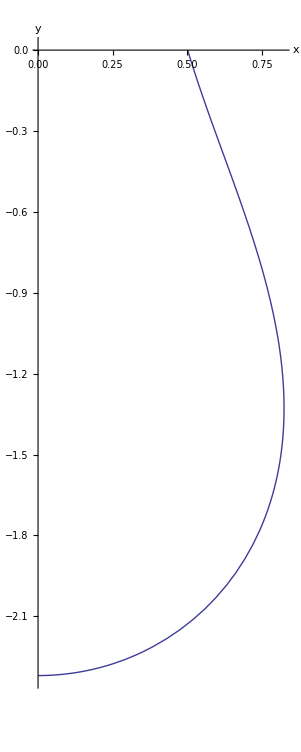

```mathematica
ParametricPlot[{x[s],y[s]}/.solforme,{s,0,Lplot},
AxesLabel-> {Style["x",FontSize->22],Style["y",FontSize->22]},LabelStyle->{FontSize->22},AspectRatio->Automatic]
```